```mathematica
(* (C) Copyright Aaron Goldberg,2022.

 This code is licensed under the Apache License,Version 2.0.You may
 obtain a copy of this license in the LICENSE.txt file in the root directory
 of this source tree or at http://www.apache.org/licenses/LICENSE-2.0.#

 Any modifications or derivative works of this code must retain this
 copyright notice,and modified files need to carry a notice indicating
 that they have been altered from the originals.
*)
```

```mathematica
(*Calculate variance of the ML estimate using method from https://iopscience.iop.org/article/10.1088/1367-2630/10/4/043022/pdf. We essentially construct the Fisher information but replacing some of the probabilities with the observed frequencies. We also hit snags when our actual probability distribution isn't normalized, because we only measure photon numbers up to something but there is some probability that the state has even more photons, so this paper takes care of it. *)

(* Now let's try using TMSV full state and using PNRDs up to some N, calculate classical FI, see how much info is there. The probability of finding k,l photons in the distribution is sum N≥ k,l  of : ((1-eta1^2)/eta1^2)^(N-k)((1-eta2^2)/eta2^2)^(N-l)(eta1 eta2 Tanh[r])^(2N)Binomial[N,k]Binomial[N,l]/Cosh[r]^2, then we also have to account for dark counts*)
maxState=100;
maxPNRD=7;(*This should be the physical maximum number of photons actually ever measured in the experiments. This is because we will normalize probabilities using the maximum that could have been found for our coefficients*)
r0=1.29995417;
eta2est=0.38206448;
eta1est=0.39202357;
v2est=0.06568101;
v1est=0.03418724;
PNRDprobs=Table[(eta1^2/(1-eta1^2))^k(eta2^2/(1-eta2^2))^l  Exp[-v1-v2]Sum[((1-eta1^2)(1-eta2^2)Tanh[r]^2)^(NN)LaguerreL[k,NN-k,v1(1-1/eta1^2)]LaguerreL[l,NN-l,v2(1-1/eta2^2)],{NN,Max[k,l],maxState}],{k,0,maxPNRD},{l,0,maxPNRD}]/Cosh[r]^2;
totalProbs=Total[PNRDprobs,2];
1-N[Total[PNRDprobs/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est,2]]
1-N[totalProbs/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est,2]
```

0.0282622

0.0282622

```mathematica
PNRDcounts={{502906140,138505888,30410854,6433943,1352221,286394,59697,15753},{
116577687,71731950,26033142,7806684,2132671,555912,137963,43721},{
23427286,23254283,12545363,5091666,1765170,558493,163976,62386},{
4664289,6420084,4657242,2430848,1039240,394509,135376,62071},{
927576,1633315,1492877,960828,494836,220903,87482,47578},{
184815,395979,437920,335277,203112,104077,47416,30694},{
36452,91856,119648,106452,74305,43590,22447,17630},{
9114,27510,42427,45106,37386,26155,15451,16884}
};(*Load the actual total data for all of the trials combined together. This is for modes 04*)
totalCounts=Total[PNRDcounts,2]
BarChart3D[(Reverse/@Log[PNRDcounts])ᵀ,ChartLayout->"Grid",AxesLabel->{"Mode 0","Mode 4","Log μ_mn"},LabelStyle->{Bold,Black,16},ChartLabels->{Table[ToString[maxPNRD-i],{i,0,maxPNRD}],Table[ToString[i],{i,0,maxPNRD}]},Method->{"Canvas"->None}]
```

1000000000

-Graphics3D-

```mathematica
(*"FI" (actually the inverse of the covariance matrix) as calculated without the approximations from the paper*) 
d1=N[D[Log[PNRDprobs/totalProbs]/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est,eta1]/.eta1-> eta1est];
d2=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.r-> r0/.v1-> v1est/.v2-> v2est,eta2]/.eta2-> eta2est];
d3=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.v1-> v1est/.v2-> v2est,r]/.r-> r0];
d4=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v2-> v2est,v1]/.v1-> v1est];
d5=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est,v2]/.v2-> v1est];
FIpap11=N[Total[d1^2*PNRDcounts,2]]
FIpap12=N[Total[d1*d2*PNRDcounts,2]]
FIpap21=FIpap12;
FIpap22=N[Total[d2^2*PNRDcounts,2]]
FIpap33=N[Total[d3^2*PNRDcounts,2]]
FIpap13=N[Total[d1*d3*PNRDcounts,2]]
FIpap31=FIpap13;
FIpap23=N[Total[d2*d3*PNRDcounts,2]]
FIpap32=FIpap23;
FIpap44=N[Total[d4^2*PNRDcounts,2]]
FIpap55=N[Total[d5^2*PNRDcounts,2]]
FIpap45=N[Total[d4*d5*PNRDcounts,2]]
FIpap54=FIpap45;
FIpap14=N[Total[d1*d4*PNRDcounts,2]]
FIpap41=FIpap14;
FIpap15=N[Total[d1*d5*PNRDcounts,2]]
FIpap51=FIpap15;
FIpap24=N[Total[d2*d4*PNRDcounts,2]]
FIpap42=FIpap24;
FIpap25=N[Total[d2*d5*PNRDcounts,2]]
FIpap52=FIpap25;
FIpap43=N[Total[d3*d4*PNRDcounts,2]]
FIpap34=FIpap43;
FIpap53=N[Total[d3*d5*PNRDcounts,2]]
FIpap35=FIpap53;


covPaperNoApprox=Inverse[{{FIpap11,FIpap12,FIpap13,FIpap14,FIpap15},{FIpap21,FIpap22,FIpap23,FIpap24,FIpap25},{FIpap31,FIpap32,FIpap33,FIpap34,FIpap35},{FIpap41,FIpap42,FIpap43,FIpap44,FIpap45},{FIpap51,FIpap52,FIpap53,FIpap54,FIpap55}}]
```

8.86676×10^9

-3.75496×10^9

9.56296×10^9

2.22796×10^9

2.21398×10^9

2.6208×10^9

1.17992×10^9

1.48649×10^9

-5.53523×10^7

2.82562×10^9

-1.0979×10^9

-8.10091×10^8

3.28762×10^9

9.73576×10^8

1.10191×10^9

{{3.97235×10^-9,3.15017×10^-9,-9.20371×10^-9,3.75684×10^-10,2.80338×10^-9},{3.15017×10^-9,3.79855×10^-9,-9.17764×10^-9,2.67559×10^-9,8.2845×10^-10},{-9.20371×10^-9,-9.17764×10^-9,2.59009×10^-8,-5.90953×10^-9,-5.91992×10^-9},{3.75684×10^-10,2.67559×10^-9,-5.90953×10^-9,6.61338×10^-9,-1.01314×10^-9},{2.80338×10^-9,8.2845×10^-10,-5.91992×10^-9,-1.01314×10^-9,5.26165×10^-9}}

```mathematica
RootMeanSquare[Flatten[PNRDcounts/totalCounts-PNRDprobs/totalProbs/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est]](*this is how well the estimator fits the data. The average count probabilities are pretty close*)
```

0.00298436

{{-0.0282034,0.147452,0.174392,0.204074,0.250576,0.322344,0.383563,0.837919},{-0.0150116,-0.0172545,0.0399886,0.0938872,0.152591,0.226789,0.290787,0.780637},{-0.0957847,-0.0754538,-0.0351797,0.0180579,0.0754813,0.145106,0.210284,0.739973},{-0.160765,-0.130678,-0.0895115,-0.0412551,0.0111135,0.0799811,0.143378,0.730769},{-0.214278,-0.181562,-0.14163,-0.0952612,-0.0441887,0.021176,0.0816641,0.710455},{-0.259387,-0.227757,-0.188367,-0.146544,-0.0968012,-0.0420593,0.0240326,0.712134},{-0.307269,-0.278959,-0.238993,-0.200713,-0.153725,-0.0979824,-0.0330756,0.757294},{-0.177626,-0.109745,-0.0309254,0.0653195,0.181522,0.335287,0.471635,2.36073}}

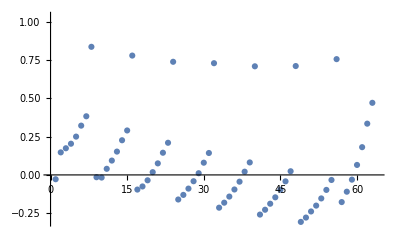

-Graphics3D-

-Graphics3D-

Average relative error is: 0.122257Average absolute relative error is: 0.24588

```mathematica
relativeerrors=((PNRDcounts/totalCounts)/(PNRDprobs/totalProbs)/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est)-1
ListPlot[Flatten[relativeerrors]]
BarChart3D[relativeerrors,ChartLayout->"Grid"]
BarChart3D[Reverse/@Abs[relativeerrorsᵀ],ChartLayout->"Grid",AxesLabel->{"Mode 0","Mode 4","ϵ"},LabelStyle-> {Bold,Black,16},ChartLabels->{Table[ToString[i],{i,0,maxPNRD}],Table[ToString[maxPNRD-i],{i,0,maxPNRD}]}]
Print["Average relative error is: ",Mean[Flatten[relativeerrors]],"Average absolute relative error is: ",Mean[Abs[Flatten[relativeerrors]]]]
```

-Graphics3D-

9.56948×10^9

-2.84813×10^9

9.59259×10^9

1.73897×10^9

2.36448×10^9

2.42217×10^9

1.85516×10^9

2.05736×10^9

-8.64524×10^7

3.80646×10^9

-9.53419×10^8

-8.35382×10^8

3.98516×10^9

1.11979×10^9

1.17227×10^9

{{6.81812×10^-9,5.85972×10^-9,-2.09377×10^-8,1.46436×10^-9,3.80085×10^-9},{5.85972×10^-9,6.58565×10^-9,-2.06628×10^-8,3.50221×10^-9,1.87953×10^-9},{-2.09377×10^-8,-2.06628×10^-8,7.18956×10^-8,-1.02569×10^-8,-1.10751×10^-8},{1.46436×10^-9,3.50221×10^-9,-1.02569×10^-8,5.30083×10^-9,-3.82321×10^-11},{3.80085×10^-9,1.87953×10^-9,-1.10751×10^-8,-3.82321×10^-11,4.91562×10^-9}}

0.00250437

{{-0.0258172,0.0968164,0.0790103,0.0665102,0.0707356,0.0914893,0.117881,0.388641},{0.0349591,-0.0103942,-0.00165122,0.00829734,0.0203418,0.0453535,0.0768234,0.392042},{-0.0174724,-0.035735,-0.0323175,-0.0181307,-0.0058072,0.0257238,0.0542145,0.373555},{-0.0585588,-0.0588938,-0.0517584,-0.0398475,-0.0238618,-0.0020262,0.0318752,0.355651},{-0.0746631,-0.0664992,-0.0577896,-0.04079,-0.0293158,-0.0206753,0.0301746,0.401743},{-0.0861525,-0.0794384,-0.0675216,-0.0485371,-0.0347602,-0.0199256,0.0367231,0.457195},{-0.0901207,-0.0730069,-0.0481331,-0.0264144,-0.0130143,-0.00268176,0.0583137,0.605687},{0.0494244,0.052418,0.132641,0.186128,0.303767,0.356501,0.527853,1.47771}}

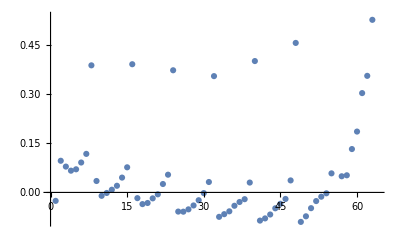

-Graphics3D-

-Graphics3D-

Average relative error is: 0.0897576Average absolute relative error is: 0.129186

```mathematica
(*Now do modes 15*)
PNRDcounts={{586316560,133704399,23751898,4045986,685584,116822,19910,4107},{
120917224,54527109,15380159,3655658,795719,166110,33642,8338},{
20540767,14559005,5914518,1863793,506959,128160,30303,8677},{
3409203,3335853,1787759,709857,235782,69821,19205,6302},{
572400,716064,478133,231767,90882,30858,9864,3776},{
95975,145427,116776,66934,30550,11943,4335,1914},{
16180,29179,27709,18375,9564,4200,1709,902},{
3156,6447,7337,5652,3589,1811,866,537}
};(*Load the actual total data for all of the trials combined together. This is for modes 15*)
BarChart3D[(Reverse/@Log[PNRDcounts])ᵀ,ChartLayout->"Grid",AxesLabel->{"Mode 1","Mode 5","Log  μ_mn"},LabelStyle->{Bold,Black,16},ChartLabels->{Table[ToString[maxPNRD-i],{i,0,maxPNRD}],Table[ToString[i],{i,0,maxPNRD}]},Method->{"Canvas"->None}]
r0=1.32379823;
eta2est=0.30441043;
eta1est=0.30706105;
v2est=0.05945008;
v1est=0.04066411;

maxPNRD=7;(*(*If we keep fewer than the total, the FI gets smaller and we get closer to realistic results. This is because the relative error for the high PNRDs is rather large for these modes, because not enough statistics there. Should always just ignore some top values probably*)
PNRDcounts=PNRDcounts[[1;;maxPNRD+1,1;;maxPNRD+1]];*)
maxState=100;
totalCounts=Total[PNRDcounts,2];

PNRDprobs=Table[(eta1^2/(1-eta1^2))^k(eta2^2/(1-eta2^2))^l  Exp[-v1-v2]Sum[((1-eta1^2)(1-eta2^2)Tanh[r]^2)^(NN)LaguerreL[k,NN-k,v1(1-1/eta1^2)]LaguerreL[l,NN-l,v2(1-1/eta2^2)],{NN,Max[k,l],maxState}],{k,0,maxPNRD},{l,0,maxPNRD}]/Cosh[r]^2;totalProbs=Total[PNRDprobs,2];

(*"FI" (actually the inverse of the covariance matrix) as calculated without the approximations from the paper*) 
d1=N[D[Log[PNRDprobs/totalProbs]/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est,eta1]/.eta1-> eta1est];
d2=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.r-> r0/.v1-> v1est/.v2-> v2est,eta2]/.eta2-> eta2est];
d3=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.v1-> v1est/.v2-> v2est,r]/.r-> r0];
d4=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v2-> v2est,v1]/.v1-> v1est];
d5=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est,v2]/.v2-> v1est];
FIpap11=N[Total[d1^2*PNRDcounts,2]]
FIpap12=N[Total[d1*d2*PNRDcounts,2]]
FIpap21=FIpap12;
FIpap22=N[Total[d2^2*PNRDcounts,2]]
FIpap33=N[Total[d3^2*PNRDcounts,2]]
FIpap13=N[Total[d1*d3*PNRDcounts,2]]
FIpap31=FIpap13;
FIpap23=N[Total[d2*d3*PNRDcounts,2]]
FIpap32=FIpap23;
FIpap44=N[Total[d4^2*PNRDcounts,2]]
FIpap55=N[Total[d5^2*PNRDcounts,2]]
FIpap45=N[Total[d4*d5*PNRDcounts,2]]
FIpap54=FIpap45;
FIpap14=N[Total[d1*d4*PNRDcounts,2]]
FIpap41=FIpap14;
FIpap15=N[Total[d1*d5*PNRDcounts,2]]
FIpap51=FIpap15;
FIpap24=N[Total[d2*d4*PNRDcounts,2]]
FIpap42=FIpap24;
FIpap25=N[Total[d2*d5*PNRDcounts,2]]
FIpap52=FIpap25;
FIpap43=N[Total[d3*d4*PNRDcounts,2]]
FIpap34=FIpap43;
FIpap53=N[Total[d3*d5*PNRDcounts,2]]
FIpap35=FIpap53;


covPaperNoApprox=Inverse[{{FIpap11,FIpap12,FIpap13,FIpap14,FIpap15},{FIpap21,FIpap22,FIpap23,FIpap24,FIpap25},{FIpap31,FIpap32,FIpap33,FIpap34,FIpap35},{FIpap41,FIpap42,FIpap43,FIpap44,FIpap45},{FIpap51,FIpap52,FIpap53,FIpap54,FIpap55}}]



RootMeanSquare[Flatten[PNRDcounts/totalCounts-PNRDprobs/totalProbs/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est]](*this is how well the estimator fits the data. The average count probabilities are pretty close*)

relativeerrors=((PNRDcounts/totalCounts)/(PNRDprobs/totalProbs)/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est)-1
ListPlot[Flatten[relativeerrors]]
BarChart3D[relativeerrors,ChartLayout->"Grid"]
BarChart3D[Reverse/@Abs[relativeerrorsᵀ],ChartLayout->"Grid",AxesLabel->{"Mode 1","Mode 5","ϵ"},LabelStyle-> {Bold,Black,16},ChartLabels->{Table[ToString[i],{i,0,maxPNRD}],Table[ToString[maxPNRD-i],{i,0,maxPNRD}]}]
Print["Average relative error is: ",Mean[Flatten[relativeerrors]],"Average absolute relative error is: ",Mean[Abs[Flatten[relativeerrors]]]]
```

-Graphics3D-

1000000000

8.79907×10^9

-3.15399×10^9

8.14868×10^9

2.07034×10^9

2.39568×10^9

2.20176×10^9

1.41916×10^9

1.38643×10^9

-4.71593×10^7

3.14768×10^9

-8.43695×10^8

-8.63401×10^8

2.96355×10^9

1.0738×10^9

1.04026×10^9

{{4.15381×10^-9,3.17399×10^-9,-1.01156×10^-8,4.83108×10^-10,3.34949×10^-9},{3.17399×10^-9,4.03702×10^-9,-9.92543×10^-9,2.95446×10^-9,8.49882×10^-10},{-1.01156×10^-8,-9.92543×10^-9,2.9996×10^-8,-6.55347×10^-9,-7.66904×10^-9},{4.83108×10^-10,2.95446×10^-9,-6.55347×10^-9,6.35972×10^-9,-8.87801×10^-10},{3.34949×10^-9,8.49882×10^-10,-7.66904×10^-9,-8.87801×10^-10,6.6669×10^-9}}

0.00276578

{{-0.0365148,0.0809734,0.0197122,-0.04025,-0.0819978,-0.117262,-0.1332,-0.108017,-0.209994},{0.0923888,-0.0140353,-0.0401385,-0.0705534,-0.0950217,-0.117546,-0.132394,-0.0839836,-0.209142},{0.0775719,-0.000726747,-0.0424031,-0.066723,-0.0844058,-0.103182,-0.122311,-0.0445125,-0.148419},{0.0713528,0.0143191,-0.0223316,-0.0469356,-0.0661191,-0.0872369,-0.095868,-0.0224581,-0.0761582},{0.0859798,0.0369364,0.00482578,-0.0178734,-0.0339623,-0.0519661,-0.064355,0.0148011,0.0285228},{0.112297,0.0667766,0.0418311,0.0147858,0.00201717,-0.0119981,-0.029178,0.0684581,0.11549},{0.146682,0.111711,0.0842351,0.0594937,0.0566191,0.0232173,0.0429966,0.124676,0.312492},{0.166391,0.144895,0.130102,0.0941788,0.0743465,0.0798052,0.0620421,0.248645,0.339626},{0.602608,0.565097,0.567164,0.648444,0.657477,0.715397,0.826544,1.16769,2.04934}}

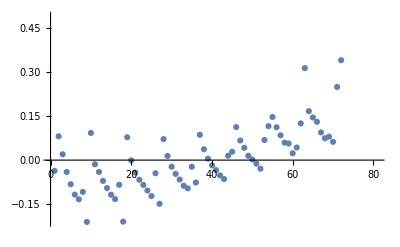

-Graphics3D-

-Graphics3D-

Average relative error is: 0.102738Average absolute relative error is: 0.170125

```mathematica
(*Now do modes 26*)
PNRDcounts={{524756346,134833740,26480529,4965708,925565,171427,32222,6326,1067},{
127450820,67575821,21495529,5684091,1376126,315266,70147,16325,3047},{
24993605,21197861,9944573,3546466,1090694,303820,79125,21849,4764},{
4773075,5637740,3551795,1628170,615979,204337,62747,19673,5123},{
913644,1383688,1101565,622687,283884,110979,39112,13952,4363},{
175181,324081,313937,210724,113120,51312,20500,8345,2991},{
33656,74224,84248,65991,41179,20881,9746,4335,1920},{
6365,16385,21620,19157,13337,7890,3962,2126,951},{
1624,4713,7128,7719,6157,4171,2506,1491,955}
};(*Load the actual total data for all of the trials combined together. This is for modes 26*)
maxPNRD=8;(*This should be the physical maximum number of photons actually ever measured in the experiments. This is because we will normalize probabilities using the maximum that could have been found for our coefficients*)
BarChart3D[(Reverse/@Log[PNRDcounts])ᵀ,ChartLayout->"Grid",AxesLabel->{"Mode 2","Mode 6","Log  μ_mn"},LabelStyle->{Bold,Black,16},ChartLabels->{Table[ToString[maxPNRD-i],{i,0,maxPNRD}],Table[ToString[i],{i,0,maxPNRD}]},Method->{"Canvas"->None}]
PNRDprobs=Table[(eta1^2/(1-eta1^2))^k(eta2^2/(1-eta2^2))^l  Exp[-v1-v2]Sum[((1-eta1^2)(1-eta2^2)Tanh[r]^2)^(NN)LaguerreL[k,NN-k,v1(1-1/eta1^2)]LaguerreL[l,NN-l,v2(1-1/eta2^2)],{NN,Max[k,l],maxState}],{k,0,maxPNRD},{l,0,maxPNRD}]/Cosh[r]^2;totalProbs=Total[PNRDprobs,2];
r0=1.26655155;
eta2est=0.37228949;
eta1est=0.36837497;
v2est=0.07195477;
v1est=0.05311497;
totalCounts=Total[PNRDcounts,2]



(*"FI" (actually the inverse of the covariance matrix) as calculated without the approximations from the paper*) 
d1=N[D[Log[PNRDprobs/totalProbs]/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est,eta1]/.eta1-> eta1est];
d2=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.r-> r0/.v1-> v1est/.v2-> v2est,eta2]/.eta2-> eta2est];
d3=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.v1-> v1est/.v2-> v2est,r]/.r-> r0];
d4=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v2-> v2est,v1]/.v1-> v1est];
d5=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est,v2]/.v2-> v1est];
FIpap11=N[Total[d1^2*PNRDcounts,2]]
FIpap12=N[Total[d1*d2*PNRDcounts,2]]
FIpap21=FIpap12;
FIpap22=N[Total[d2^2*PNRDcounts,2]]
FIpap33=N[Total[d3^2*PNRDcounts,2]]
FIpap13=N[Total[d1*d3*PNRDcounts,2]]
FIpap31=FIpap13;
FIpap23=N[Total[d2*d3*PNRDcounts,2]]
FIpap32=FIpap23;
FIpap44=N[Total[d4^2*PNRDcounts,2]]
FIpap55=N[Total[d5^2*PNRDcounts,2]]
FIpap45=N[Total[d4*d5*PNRDcounts,2]]
FIpap54=FIpap45;
FIpap14=N[Total[d1*d4*PNRDcounts,2]]
FIpap41=FIpap14;
FIpap15=N[Total[d1*d5*PNRDcounts,2]]
FIpap51=FIpap15;
FIpap24=N[Total[d2*d4*PNRDcounts,2]]
FIpap42=FIpap24;
FIpap25=N[Total[d2*d5*PNRDcounts,2]]
FIpap52=FIpap25;
FIpap43=N[Total[d3*d4*PNRDcounts,2]]
FIpap34=FIpap43;
FIpap53=N[Total[d3*d5*PNRDcounts,2]]
FIpap35=FIpap53;


covPaperNoApprox=Inverse[{{FIpap11,FIpap12,FIpap13,FIpap14,FIpap15},{FIpap21,FIpap22,FIpap23,FIpap24,FIpap25},{FIpap31,FIpap32,FIpap33,FIpap34,FIpap35},{FIpap41,FIpap42,FIpap43,FIpap44,FIpap45},{FIpap51,FIpap52,FIpap53,FIpap54,FIpap55}}]



RootMeanSquare[Flatten[PNRDcounts/totalCounts-PNRDprobs/totalProbs/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est]](*this is how well the estimator fits the data. The average count probabilities are pretty close*)

relativeerrors=((PNRDcounts/totalCounts)/(PNRDprobs/totalProbs)/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est)-1
ListPlot[Flatten[relativeerrors]]
BarChart3D[relativeerrors,ChartLayout->"Grid"]
BarChart3D[Reverse/@Abs[relativeerrorsᵀ],ChartLayout->"Grid",AxesLabel->{"Mode 2","Mode 6","ϵ"},LabelStyle-> {Bold,Black,16},ChartLabels->{Table[ToString[i],{i,0,maxPNRD}],Table[ToString[maxPNRD-i],{i,0,maxPNRD}]}]
Print["Average relative error is: ",Mean[Flatten[relativeerrors]],"Average absolute relative error is: ",Mean[Abs[Flatten[relativeerrors]]]]
```

-Graphics3D-

1000000000

1.01907×10^10

-2.7081×10^9

9.51306×10^9

1.61951×10^9

2.42378×10^9

2.33746×10^9

2.09432×10^9

2.43208×10^9

-1.16757×10^8

4.19968×10^9

-1.02513×10^9

-8.45209×10^8

4.2846×10^9

1.15784×10^9

1.20889×10^9

{{7.5618×10^-9,6.56896×10^-9,-2.48412×10^-8,1.44573×10^-9,4.0317×10^-9},{6.56896×10^-9,7.16265×10^-9,-2.42968×10^-8,3.28349×10^-9,2.38495×10^-9},{-2.48412×10^-8,-2.42968×10^-8,8.98926×10^-8,-1.04055×10^-8,-1.28484×10^-8},{1.44573×10^-9,3.28349×10^-9,-1.04055×10^-8,4.66851×10^-9,2.211×10^-10},{4.0317×10^-9,2.38495×10^-9,-1.28484×10^-8,2.211×10^-10,4.306×10^-9}}

0.00260461

{{-0.0279341,0.104728,0.0855228,0.0415319,0.0150292,0.0568108,0.183317,0.127486,-0.0235691},{0.0316601,-0.00929041,-0.0106391,-0.0250567,-0.0343362,0.00465914,0.137194,0.0518894,-0.287291},{-0.0110671,-0.0288052,-0.0365004,-0.0446768,-0.049471,-0.0152087,0.0972559,0.0568027,-0.28036},{-0.0339467,-0.0390618,-0.0407929,-0.0462029,-0.0471715,-0.011491,0.111495,0.0509804,-0.196993},{-0.0434723,-0.0405307,-0.0351384,-0.0350283,-0.0330499,0.00356425,0.136144,0.134983,-0.143323},{-0.0452769,-0.0298713,-0.0223963,-0.0259466,-0.0227353,0.0402416,0.180466,0.152196,-0.0993494},{0.00284584,0.0101691,0.0137767,0.0234113,0.0341515,0.128335,0.137987,0.373704,0.239073},{0.242165,0.24054,0.292622,0.370128,0.39789,0.493059,0.720155,0.896344,1.31622}}

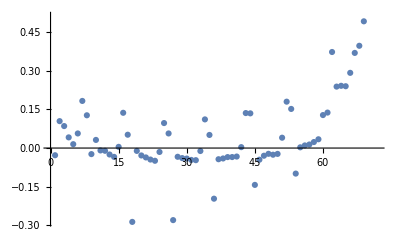

-Graphics3D-

-Graphics3D-

Average relative error is: 0.0813965Average absolute relative error is: 0.133507

```mathematica
(*Now do modes 37. Because the max photon number is different in each mode, we need to take a bit more care here!*)
PNRDcounts={{594595127,141330013,24834616,4001949,636732,106804,19146,2912,402},{
115671925,51741202,14208472,3209658,662500,135647,29105,4971,610},{
18751261,12873928,5026049,1501460,388290,95189,23531,4799,668},{
3004170,2803544,1433995,539433,169810,49185,14173,3223,564},{
481797,570935,363643,166217,62022,20828,6890,1862,358},{
77488,112364,85545,45769,19786,7775,2905,855,188},{
13087,22069,19453,12130,6009,2725,1009,406,113},{
2604,4998,5216,3864,2169,1072,501,202,83},{
0,0,0,0,0,0,0,0,0}

};(*Load the actual total data for all of the trials combined together. This is for modes 37*)
PNRDcounts={{594595127,141330013,24834616,4001949,636732,106804,19146,2912,402},{
115671925,51741202,14208472,3209658,662500,135647,29105,4971,610},{
18751261,12873928,5026049,1501460,388290,95189,23531,4799,668},{
3004170,2803544,1433995,539433,169810,49185,14173,3223,564},{
481797,570935,363643,166217,62022,20828,6890,1862,358},{
77488,112364,85545,45769,19786,7775,2905,855,188},{
13087,22069,19453,12130,6009,2725,1009,406,113},{
2604,4998,5216,3864,2169,1072,501,202,83}
};(*Remove the final row!*)
maxPNRD=8;
BarChart3D[(Reverse/@Log[PNRDcounts])ᵀ,ChartLayout->"Grid",AxesLabel->{"Mode 3","Mode 7","Log μ_mn"},LabelStyle->{Bold,Black,16},ChartLabels->{Table[ToString[maxPNRD-i],{i,0,maxPNRD}],Table[ToString[i],{i,0,maxPNRD}]},Method->{"Canvas"->None}]
maxState=100;(*This should be the physical maximum number of photons actually ever measured in the experiments. This is because we will normalize probabilities using the maximum that could have been found for our coefficients*)
PNRDprobs=Table[(eta1^2/(1-eta1^2))^k(eta2^2/(1-eta2^2))^l  Exp[-v1-v2]Sum[((1-eta1^2)(1-eta2^2)Tanh[r]^2)^(NN)LaguerreL[k,NN-k,v1(1-1/eta1^2)]LaguerreL[l,NN-l,v2(1-1/eta2^2)],{NN,Max[k,l],maxState}],{k,0,maxPNRD-1},{l,0,maxPNRD}]/Cosh[r]^2;(*NOTE the -1*)
totalProbs=Total[PNRDprobs,2];
r0=1.34247064;
eta2est=0.28621032;
eta1est=0.2872952;
v2est=0.07790762;
v1est=0.03552011;
totalCounts=Total[PNRDcounts,2]



(*"FI" (actually the inverse of the covariance matrix) as calculated without the approximations from the paper*) 
d1=N[D[Log[PNRDprobs/totalProbs]/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est,eta1]/.eta1-> eta1est];
d2=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.r-> r0/.v1-> v1est/.v2-> v2est,eta2]/.eta2-> eta2est];
d3=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.v1-> v1est/.v2-> v2est,r]/.r-> r0];
d4=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v2-> v2est,v1]/.v1-> v1est];
d5=N[D[Log[PNRDprobs/totalProbs]/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est,v2]/.v2-> v1est];
FIpap11=N[Total[d1^2*PNRDcounts,2]]
FIpap12=N[Total[d1*d2*PNRDcounts,2]]
FIpap21=FIpap12;
FIpap22=N[Total[d2^2*PNRDcounts,2]]
FIpap33=N[Total[d3^2*PNRDcounts,2]]
FIpap13=N[Total[d1*d3*PNRDcounts,2]]
FIpap31=FIpap13;
FIpap23=N[Total[d2*d3*PNRDcounts,2]]
FIpap32=FIpap23;
FIpap44=N[Total[d4^2*PNRDcounts,2]]
FIpap55=N[Total[d5^2*PNRDcounts,2]]
FIpap45=N[Total[d4*d5*PNRDcounts,2]]
FIpap54=FIpap45;
FIpap14=N[Total[d1*d4*PNRDcounts,2]]
FIpap41=FIpap14;
FIpap15=N[Total[d1*d5*PNRDcounts,2]]
FIpap51=FIpap15;
FIpap24=N[Total[d2*d4*PNRDcounts,2]]
FIpap42=FIpap24;
FIpap25=N[Total[d2*d5*PNRDcounts,2]]
FIpap52=FIpap25;
FIpap43=N[Total[d3*d4*PNRDcounts,2]]
FIpap34=FIpap43;
FIpap53=N[Total[d3*d5*PNRDcounts,2]]
FIpap35=FIpap53;


covPaperNoApprox=Inverse[{{FIpap11,FIpap12,FIpap13,FIpap14,FIpap15},{FIpap21,FIpap22,FIpap23,FIpap24,FIpap25},{FIpap31,FIpap32,FIpap33,FIpap34,FIpap35},{FIpap41,FIpap42,FIpap43,FIpap44,FIpap45},{FIpap51,FIpap52,FIpap53,FIpap54,FIpap55}}]



RootMeanSquare[Flatten[PNRDcounts/totalCounts-PNRDprobs/totalProbs/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est]](*this is how well the estimator fits the data. The average count probabilities are pretty close*)

relativeerrors=((PNRDcounts/totalCounts)/(PNRDprobs/totalProbs)/.eta1-> eta1est/.eta2-> eta2est/.r-> r0/.v1-> v1est/.v2-> v2est)-1
ListPlot[Flatten[relativeerrors]]
BarChart3D[relativeerrors,ChartLayout->"Grid"]
BarChart3D[Reverse/@Abs[relativeerrorsᵀ],ChartLayout->"Grid",AxesLabel->{"Mode 3","Mode 7","ϵ"},LabelStyle-> {Bold,Black,16},ChartLabels->{Table[ToString[i],{i,0,maxPNRD}],Table[ToString[maxPNRD-1-i],{i,0,maxPNRD-1}]}](*NOTE the -1*)
Print["Average relative error is: ",Mean[Flatten[relativeerrors]],"Average absolute relative error is: ",Mean[Abs[Flatten[relativeerrors]]]]
```